```mathematica
Clear["Global`*"]
```

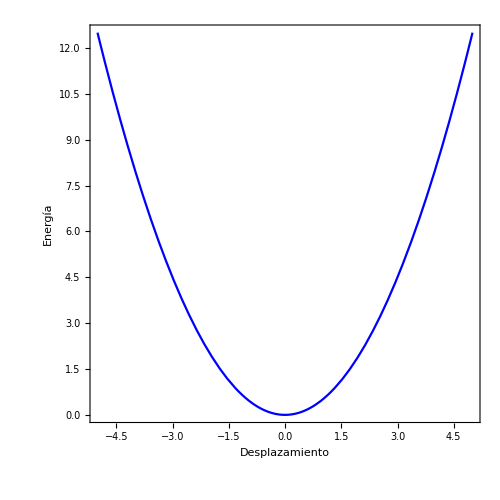

```mathematica
V[x_]= 1/2 Subscript[k, f] x^2;
conditions={Subscript[k, f]->1,m->1,ℏ->1};
PlotEnergiaPotencial =
Plot[V[x] /. conditions,{x,-5,5},Frame->True,PlotStyle->Blue, AspectRatio->1,FrameLabel->{"Desplazamiento","Energía"},LabelStyle->Directive[16,Black],Background->White,FrameStyle->Directive[Background->White],ImageSize->500]
```

```mathematica
Ψ[v_,x_]=Module[{α, y}, α=(ℏ^2/(m Subscript[k, f]));
y=x/α;
ConditionalExpression[√(1/(α π^(1/2)2^v v!))HermiteH[v,y] ⅇ^(-y^2/2), v ∈Integers && v ≥ 0]];
Ψ[2,x]
```

(ⅇ^(-(m^2 x^2 k_f^2)/(2 ℏ^4)) √((m k_f)/ℏ^2) (-2+(4 m^2 x^2 k_f^2)/ℏ^4))/(2 √2 π^(1/4))

```mathematica
Ψ[0,x]/.conditions
Ψ[1,x]/.conditions
Ψ[2,x]/.conditions
Ψ[3,x]/.conditions
Ψ[4,x]/.conditions
Ψ[5,x]/.conditions
```

(ⅇ^(-x^2/2))/π^(1/4)

(√2 ⅇ^(-x^2/2) x)/π^(1/4)

(ⅇ^(-x^2/2) (-2+4 x^2))/(2 √2 π^(1/4))

(ⅇ^(-x^2/2) (-12 x+8 x^3))/(4 √3 π^(1/4))

(ⅇ^(-x^2/2) (12-48 x^2+16 x^4))/(8 √6 π^(1/4))

(ⅇ^(-x^2/2) (120 x-160 x^3+32 x^5))/(16 √15 π^(1/4))

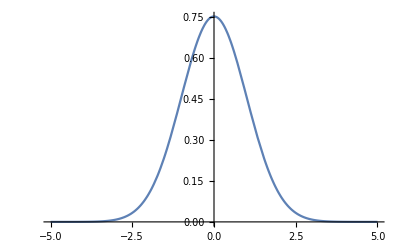

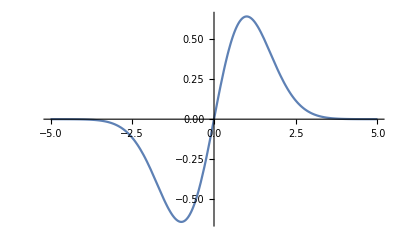

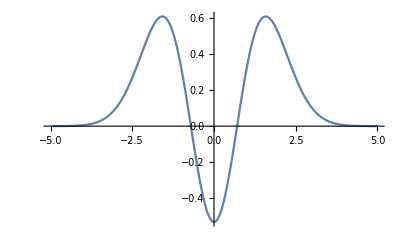

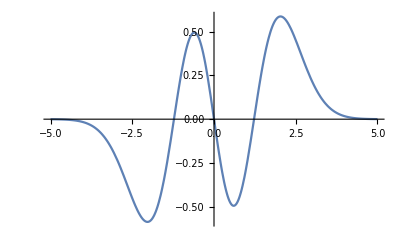

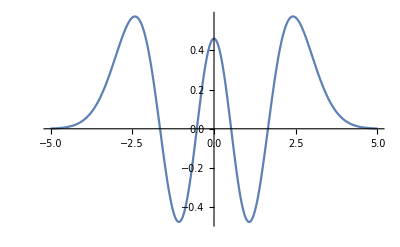

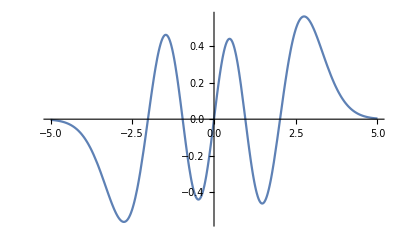

```mathematica
Plot[Ψ[0,x]/.conditions/.conditions,{x,-5,5}]
Plot[Ψ[1,x]/.conditions/.conditions,{x,-5,5}]
Plot[Ψ[2,x]/.conditions/.conditions,{x,-5,5}]
Plot[Ψ[3,x]/.conditions/.conditions,{x,-5,5}]
Plot[Ψ[4,x]/.conditions/.conditions,{x,-5,5}]
Plot[Ψ[5,x]/.conditions/.conditions,{x,-5,5}]
```

```mathematica
Energy[v_]=ConditionalExpression[(v+1/2)ℏ √(Subscript[k, f]/m),v∈Integers && v ≥0];
Table[Energy[v],{v,0,10}]
Table[Energy[v],{v,0,10}]/.conditions
```

{1/2 ℏ √(k_f/m),3/2 ℏ √(k_f/m),5/2 ℏ √(k_f/m),7/2 ℏ √(k_f/m),9/2 ℏ √(k_f/m),11/2 ℏ √(k_f/m),13/2 ℏ √(k_f/m),15/2 ℏ √(k_f/m),17/2 ℏ √(k_f/m),19/2 ℏ √(k_f/m),21/2 ℏ √(k_f/m)}

{1/2,3/2,5/2,7/2,9/2,11/2,13/2,15/2,17/2,19/2,21/2}

```mathematica
xCrossings[v_]:=x/.Solve[(Energy[v]==V[x])/.conditions]
Table[xCrossings[v],{v,0,10}]
```

{{-1,1},{-√3,√3},{-√5,√5},{-√7,√7},{-3,3},{-√11,√11},{-√13,√13},{-√15,√15},{-√17,√17},{-√19,√19},{-√21,√21}}

```mathematica
Solve[Energy[3]==V[x],x]
```

{{x→-(√7 √ℏ (k_f/m)^(1/4))/(√k_f)},{x→(√7 √ℏ (k_f/m)^(1/4))/(√k_f)}}

```mathematica
Solve[(Energy[3]==V[x])/.conditions,x]
```

{{x→-√7},{x→√7}}

```mathematica
x/.{{x->-√7},{x->√7}}
```

{-√7,√7}

```mathematica
x/.Solve[(Energy[3]==V[x])/.conditions,x]
```

{-√7,√7}

```mathematica
xCrossings[v]:=x/.Solve[(Energy[v]==V[x])/.conditions,x]
```

```mathematica
FuncionOnda[v_,x_]=(1.5 Ψ[v,x])/.conditions
```

ConditionalExpression[1.12669 ⅇ^(-x^2/2) √(2^-v/(v!)) HermiteH[v,x], v∈ℤ&&v≥0]

```mathematica
ConditionalExpression[1.1266883166974138 ⅇ^(-x^2/2) √(2^-v/(v!)) HermiteH[v,x], v∈Integers&&v≥0]
```

```mathematica
Subscript[EnergyLine, v_]:=Line[{{Subscript[xCrossings, v][[1]],Subscript[Energy, v]},{Subscript[xCrossings, v][[2]],Subscript[Energy, v]}}/.conditions]
EnergyLine1=x/.Solve[(Energy[1]==V[x])/.conditions,x]
EnergyLine2=x/.Solve[(Energy[2]==V[x])/.conditions,x]
EnergyLine3=x/.Solve[(Energy[3]==V[x])/.conditions,x]
```

{-√2 √Energy[1],√2 √Energy[1]}

{-√2 √Energy[2],√2 √Energy[2]}

{-√2 √Energy[3],√2 √Energy[3]}